```mathematica
EulerAnglesToMatrix[pyr_] := Module[{
CP = Cos[pyr[[1]]], 
SP = Sin[pyr[[1]]],
CY = Cos[pyr[[2]]],
SY = Sin[pyr[[2]]],
CR = Cos[pyr[[3]]],
SR = Sin[pyr[[3]]]
},
({{CP CY, CY SP SR-CR SY, -CR CY SP-SR SY}, {CP SY, CR CY+SP SR SY, CY SR-CR SP SY}, {SP, -CP SR, CP CR}})
]
```

```mathematica
ImportEpisode[filename_] := Module[{data, n , car, inputs},
data = Import[filename, "CSV"];
n = Length[data];
car = {};
inputs = {};
Do[
AppendTo[car, <|
"pos"-> data[[i,1;;3]],
"vel"-> data[[i,4;;6]],
"θ"-> EulerAnglesToMatrix[data[[i, 7;;9]] * π/32768.0],
"ω"-> data[[i,10;;12]],
"sup"-> data[[i,13]],
"jump"-> data[[i,14]],
"dblj"-> data[[i,15]],
"grnd"-> data[[i,16]],
"boost"-> data[[i,17]],
"time"->0.0
|>];
AppendTo[inputs, <|
"thr"-> data[[i,18]],
"steer"-> data[[i,19]],
"pitch"-> data[[i,20]],
"yaw"-> data[[i,21]],
"roll"-> data[[i,22]],
"jump"-> data[[i,23]],
"boost"-> data[[i,24]],
"brake"-> data[[i,25]]
|>];
,
{i, 1, n}
];
{car, inputs}
]

ImportPredictions[filename_] := Module[{data, n , car},
data = Import[filename, "CSV"];
n = Length[data];
car = {};
Do[
AppendTo[car, <|
"pos"-> data[[i,1;;3]],
"vel"-> data[[i,4;;6]],
"ω"-> data[[i,7;;9]]
|>]
,
{i, 1, n}
];
car
]
```

```mathematica
drawPlots[range_] := {which = "pos";
Show[
ListLinePlot[Transpose[#[which]& /@ predictions[[range]]], PlotStyle->Dashed, PlotRange->All],
ListLinePlot[Transpose[#[which]& /@ car[[range]]], PlotRange->All],
ImageSize->Large
],

which = "vel";
Show[
ListLinePlot[Transpose[#[which]& /@ predictions[[range]]], PlotStyle->Dashed, PlotRange->All],
ListLinePlot[Transpose[#[which]& /@ car[[range]]], PlotRange->All],
ImageSize->Large
],

which = "ω";
Show[
ListLinePlot[Transpose[#[which]& /@ predictions[[range]]], PlotStyle->Dashed, PlotRange->All],
ListLinePlot[Transpose[#[which]& /@ car[[range]]], PlotRange->All],
PlotRange->All,
ImageSize->Large
]}
```

```mathematica
g = -650.0;
boostAccel = 1000.0;
timeLimit = 0.3;
ωMaxAerial= 5.5;
drivingSpeed = 1450;
brakingForce = 3500;
coastingForce = 525;
throttleThreshold = 0.05;
throttleForce = 1550;
maxSpeed = 2275;
minSpeed = 10;

κ[x_]:= Interpolation[({{0, 0.0069}, {500, 0.00398}, {1000, 0.00235}, {1500, 0.001375}, {1750, 0.0011}, {2500, 0.0008}}), InterpolationOrder->1][x]

AirDodge[state_, input_, Δt_] := Module[{
next = state

},
(* TODO *)
next
]

AerialControl[state_, input_, Δt_] := Module[{
next = state,
AirTorque = {-36.07956616966136, -12.145997819080709, 8.919628042877859},
AirDamping  = {-4.471663022015913, -2.798194258050845, -1.8864919004372327},
θ = state["θ"],
rpy = {input["roll"], input["pitch"], input["yaw"]},
ωAvg, ωLocal, T, Dd, α
},
next["vel"]=state["vel"] + ({0, 0, g}  + input["boost"] θ[[All, 1]]boostAccel)Δt;
next["pos"]=state["pos"] + next["vel"] Δt; 
T = DiagonalMatrix[AirTorque];
Dd = DiagonalMatrix[{
AirDamping[[1]], 
AirDamping[[2]](1-Abs[rpy[[2]]]), 
AirDamping[[3]](1-Abs[rpy[[3]]])
}];
next["ω"] = state["ω"] + θ.(T.rpy+ Dd.Transpose[θ].state["ω"]) Δt ;
next["ω"] *= Min[1.0, ωMaxAerial/Norm[next["ω"]]];
ωAvg = 1/2(state["ω"] + next["ω"]);
next["θ"] = RotationMatrix[Norm[ωAvg]Δt,Normalize[ωAvg]].θ;
next
]

drivingForceForward[state_, input_] := Module[{
boost=input["boost"],
steering=input["steer"],
throttle=input["thr"],
vf=(state["θ"][[All, 1]]).state["vel"],
vl=(state["θ"][[All, 2]]).state["vel"],
ωu=(state["θ"][[All, 3]]).state["ω"],
turnDamping
},
turnDamping = (-0.07186693033945346 Abs[steering]-0.055453237281917644  Abs[ωu]+0.0006255296371672214 Abs[vl]) vf;
If[boost == 1,

(* boosting *)
If[vf < 0,
brakingForce,
If[0 <vf <drivingSpeed,
(maxSpeed - Abs[vf]),
If[vf > maxSpeed,
98.25785130764065 Abs[ωu],
boostAccel +turnDamping
]
]
],

(* not boosting *)
If[throttle * Sign[vf] > -0.001 && Abs[vf] > minSpeed, 
If[Abs[throttle] <  throttleThreshold && Abs[vf] > minSpeed,
-coastingForce Sign[vf] + turnDamping,
If[Abs[vf]>drivingSpeed,
turnDamping,
throttle(throttleForce - Abs[vf]) + turnDamping
]
],
brakingForce Sign[throttle]
]
]
]

drivingForceLeft[state_, input_] := Module[{
boost=input["boost"],
steering=input["steer"],
throttle=input["thr"],
vf=(state["θ"][[All, 1]]).state["vel"],
vl=(state["θ"][[All, 2]]).state["vel"],
ωu=(state["θ"][[All, 3]]).state["ω"]
},
 (1380.4531378064655 steering+7.82811881088291 throttle-15.006402973550104 vl+668.1208332047357 ωu)(1-Exp[-0.0011607974131331873 Abs[vf]])
]

drivingTorqueUp[state_, input_] := Module[{
steering=input["steer"],
vf=(state["θ"][[All, 1]]).state["vel"],
vl=(state["θ"][[All, 2]]).state["vel"],
ωu=(state["θ"][[All, 3]]).state["ω"]
},
15(steering κ[Abs[vf]]vf- ωu)
]

GroundControl[state_, input_, Δt_] := Module[{
next = state,
forward=(state["θ"][[All, 1]]),
left=(state["θ"][[All, 2]]),
up=(state["θ"][[All, 3]]),
Fforward,Fleft,Tup
},
Fforward=drivingForceForward[state, input];
Fleft=drivingForceLeft[state, input];
Tup=drivingTorqueUp[state, input];
next["vel"]=state["vel"] + (Fforward*forward + Fleft*left) Δt;
next["pos"]=state["pos"] + next["vel"]Δt;
next["ω"]= state["ω"] + Tup*up Δt;
next["θ"]=RotationMatrix[next["ω"].up Δt, up].state["θ"];
next
]

GroundControlHandbrake[state_, input_, Δt_] := Module[{next = state},
(* TODO *)
next
]

Jump[state_, input_, Δt_] := Module[{
next = state,
θ = state["θ"]
},
next["grnd"] = 0;
next["jump"]= 1;
next["time"]= Δt;
(* TODO *)
next
]

CarControl[state_, input_, Δt_] := 
If[state["grnd"] == 1,
If[input["jump"] == 1,
Jump[state, input, Δt],
If[input["brake"] == 1,
GroundControlHandbrake[state, input, Δt],
GroundControl[state, input, Δt]
]
],
If[(input["jump"]==1)&&(state["time"]<timeLimit)&&(state["dblj"]==0),
AirDodge[state, input, Δt],
AerialControl[state, input, Δt]
]
]
```

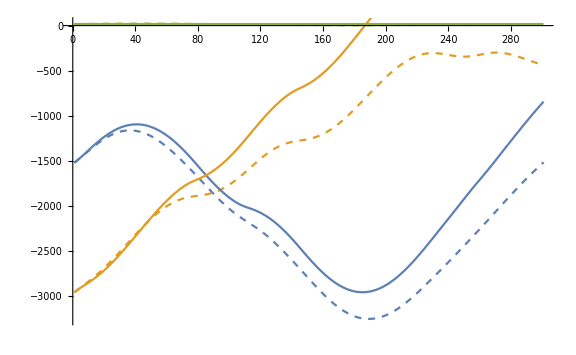
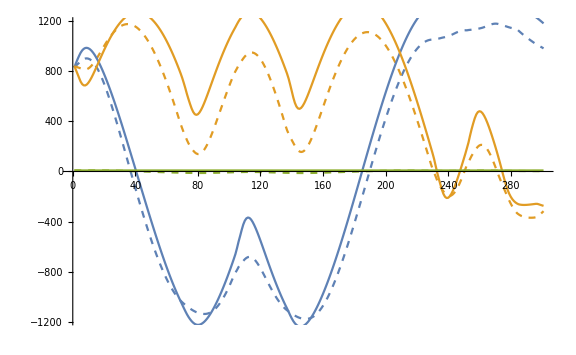
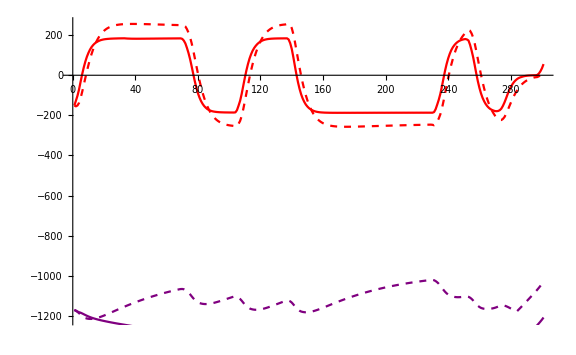
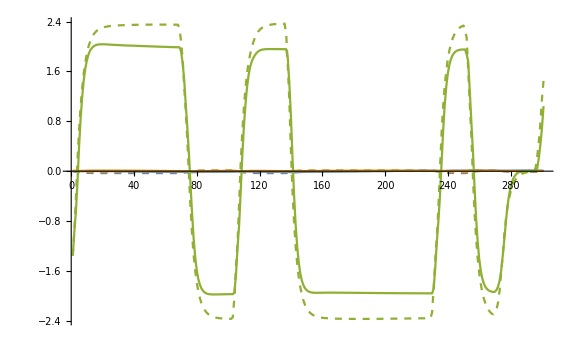

```mathematica
Δt = 0.016366612111292964;
episode=5;
directory = "ground_driving_no_handbrake";
suffix = directory <> "/episode_" <>StringPadLeft[ToString[episode], 2, "0"] <> ".csv";
filename = NotebookDirectory[] <> suffix;

{car, inputs} = ImportEpisode[filename];

predictions = {car[[1]]};
Do[
AppendTo[predictions, CarControl[predictions[[-1]], inputs[[i]], Δt]]
,
{i, 1, Length[car]-1}
]
drawPlots[]
```

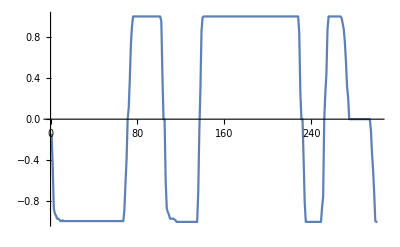

```mathematica
ListLinePlot[#["steer"]& /@ inputs]
```

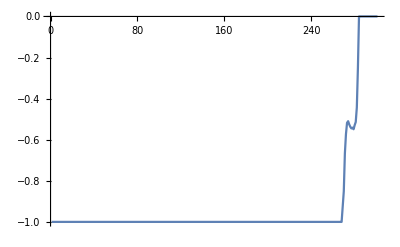

```mathematica
ListLinePlot[#["thr"]& /@ inputs]
```

```mathematica
{car, inputs} = ImportEpisode["C:\\Users\\sam\\Documents\\GitHub\\Lobot\\assets\\car_control\\ground_driving_no_handbrake\\spiral_backward_025.txt"];
v = Norm[#["vel"]] & /@ car;
vf = #["θ"][[All, 1]].#["vel"] & /@ car;
vl = #["θ"][[All, 2]].#["vel"] & /@ car;
ω = Norm[#["ω"][[3]]] & /@ car;

{car, inputs} = ImportEpisode["C:\\Users\\sam\\Documents\\GitHub\\Lobot\\assets\\car_control\\ground_driving_no_handbrake\\spiral_backward_050.txt"];
v = Join[v,Norm[#["vel"]] & /@ car];
vf = Join[vf,#["θ"][[All, 1]].#["vel"] & /@ car];
vl = Join[vl,#["θ"][[All, 2]].#["vel"] & /@ car];
ω = Join[ω,Norm[#["ω"][[3]]] & /@ car];

{car, inputs} = ImportEpisode["C:\\Users\\sam\\Documents\\GitHub\\Lobot\\assets\\car_control\\ground_driving_no_handbrake\\spiral_backward_100.txt"];
v = Join[v,Norm[#["vel"]] & /@ car];
vf = Join[vf,#["θ"][[All, 1]].#["vel"] & /@ car];
vl = Join[vl,#["θ"][[All, 2]].#["vel"] & /@ car];
ω = Join[ω,Norm[#["ω"][[3]]] & /@ car];
```

```mathematica
{car, inputs} = ImportEpisode["C:\\Users\\sam\\Documents\\GitHub\\Lobot\\assets\\car_control\\ground_driving_no_handbrake\\spiral_forward_025.txt"];
v = Join[v,Norm[#["vel"]] & /@ car];
vf = Join[vf,#["θ"][[All, 1]].#["vel"] & /@ car];
vl = Join[vl,#["θ"][[All, 2]].#["vel"] & /@ car];
ω = Join[ω,Norm[#["ω"][[3]]] & /@ car];

{car, inputs} = ImportEpisode["C:\\Users\\sam\\Documents\\GitHub\\Lobot\\assets\\car_control\\ground_driving_no_handbrake\\spiral_forward_050.txt"];
v = Join[v,Norm[#["vel"]] & /@ car];
vf = Join[vf,#["θ"][[All, 1]].#["vel"] & /@ car];
vl = Join[vl,#["θ"][[All, 2]].#["vel"] & /@ car];
ω = Join[ω,Norm[#["ω"][[3]]] & /@ car];

{car, inputs} = ImportEpisode["C:\\Users\\sam\\Documents\\GitHub\\Lobot\\assets\\car_control\\ground_driving_no_handbrake\\spiral_forward_100.txt"];
v = Join[v,Norm[#["vel"]] & /@ car];
vf = Join[vf,#["θ"][[All, 1]].#["vel"] & /@ car];
vl = Join[vl,#["θ"][[All, 2]].#["vel"] & /@ car];
ω = Join[ω,Norm[#["ω"][[3]]] & /@ car];
```

```mathematica
{car, inputs} = ImportEpisode["C:\\Users\\sam\\Documents\\GitHub\\Lobot\\assets\\car_control\\ground_driving_no_handbrake\\spiral_forward_100.txt"];
v = Norm[#["vel"]] & /@ car;
vf = #["θ"][[All, 1]].#["vel"] & /@ car;
vl =#["θ"][[All, 2]].#["vel"] & /@ car;
ω = Norm[#["ω"][[3]]] & /@ car;
```

```mathematica
κ[2300] * 2300
```

2.024

```mathematica
κ[1410] * 1410
```

2.18621

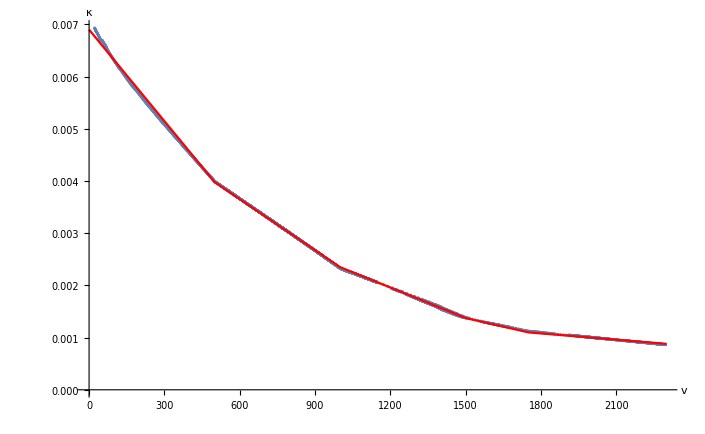

```mathematica
Show[
ListPlot[Transpose[{vf, ω/vf}], AxesLabel->{"v", "κ"}],
Plot[κ[x], {x, 0, 2300}, PlotStyle->Red]
]
```